```mathematica
Needs["ErrorBarPlots`"];
```

The model

Use plain frequencies instead of angular frequncies throughout this file

```mathematica
ParNames={"x0","A","s","τ"};
Fixed={False,False,False,False};
StartValue={15.2,12,0.1,1};
ParMax=Length[ParNames];
UseErr=True;
```

```mathematica
f[x_,x0_,A_,s_,τ_]:=A*Exp[-(x-x0)/τ] (1+Erf[(x-x0)/s-s/(2 τ)]);
```

This fit function is impirical.
It is obtained by convoluting an exponential decay Exp[-x/τ] for x>0 and zero otherwise
with a Gaussian Exp[-x^2/s^2]

Import data
Columns: 1=x, 2=y, 3=yerr

```mathematica
XCol=1;
YCol=2;
YErrCol=3;
```

```mathematica
MyData=Import["D:/Temp/memory_CountsLR_120117.txt","Table"];
```

```mathematica
Ind=1;
TheData[Ind]=MyData;
MinTime=Part[First[TheData[Ind]],XCol];
MaxTime=Part[Last[TheData[Ind]],XCol];
If[Length[Transpose[TheData[Ind]]]==2||YErrCol==0,UseErr=False;];
```

```mathematica
TheData[Ind]=Select[TheData[Ind],MinTime≤Part[#1,XCol]≤MaxTime&];
```

```mathematica
X[TheTab_]:=Part[TheTab,All,XCol];
Y[TheTab_]:=Part[TheTab,All,YCol];
Err[TheTab_]:=Part[TheTab,All,YErrCol];
DataOnly[TheTab_]:=Part[TheTab,All,{XCol,YCol}];
DataAndErr[TheTab_]:=Table[{{Part[TheTab,Ind,XCol],Part[TheTab,Ind,YCol]},ErrorBar[Part[TheTab,Ind,YErrCol]]},{Ind,Length[TheTab]}];
WeightFunc[x_]:=x^-2;
MyWeights[TheTab_]:=WeightFunc[Part[TheTab,All,YErrCol]];
```

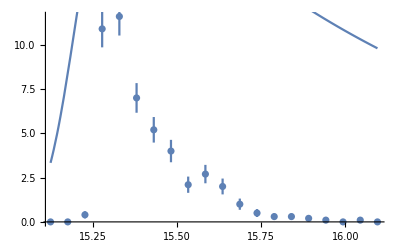

```mathematica
If[UseErr
,(DataPlot=ErrorListPlot[DataAndErr[TheData[Ind]],PlotRange->All]);
,(DataPlot=ListPlot[DataOnly[TheData[Ind]],PlotStyle->PointSize[0.02],PlotRange->All]);]
StartPlot=Plot[Apply[f,Prepend[StartValue,t]],{t,MinTime,MaxTime}];
Show[DataPlot,StartPlot]
```

```mathematica
ParamRepl=Table[P[x]->Part[ParNames,x],{x,ParMax}];
Q[x_]:=If[Part[Fixed,x],Part[StartValue,x],P[x]];
QQTab={};
Do[If[Not[Part[Fixed,x]],AppendTo[QQTab,{P[x],Part[StartValue,x]}]];,{x,ParMax}];
QQIndTab=Prepend[Table[Q[x],{x,ParMax}],t];
FitParIndTab=Prepend[Table[FitPar[x],{x,ParMax}],t];
```

```mathematica
TheFit[Ind]=
If[UseErr
,NonlinearModelFit[DataOnly[TheData[Ind]],Apply[f,QQIndTab],QQTab,t,MaxIterations->100,Weights->MyWeights[TheData[Ind]]]
,NonlinearModelFit[DataOnly[TheData[Ind]],Apply[f,QQIndTab],QQTab,t,MaxIterations->100]];
```

| Estimate | Standard Error | Confidence Interval
x0 | 15.2661 | 0.00298143 | {15.2598,15.2724}
A | 8.73948 | 0.524772 | {7.62701,9.85195}
s | 0.0279521 | 0.00261769 | {0.0224029,0.0335014}
τ | 0.139662 | 0.00639471 | {0.126106,0.153218}

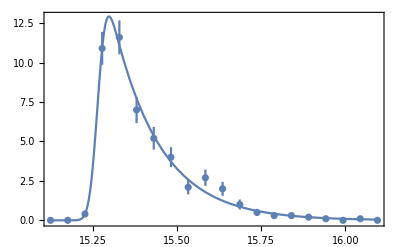

χ^2 = 10.4561        DoF = 16

χ^2/DoF = 0.653507

The fit residuals scatter LESS than (the most likely value of the PDF) expect from the error bars.

One needs to consider the following confidence interval to accomodate the fit residuals in a χ^2 distribution.

The 0.533215 confidence interval (cutting off at equal values of the PDF).

The 0.683498 confidence interval (cutting off at equal values of the CDF, which is less standard).

A value near unity here implies that the fit residuals are unlikely to be explained by statistical scatter.

A value near zero here might be coincidence but it might also indicate that the dataset overestimated the error bars.

```mathematica
Print[TheFit[Ind]["ParameterConfidenceIntervalTable"]/.ParamRepl];
FitPlot=Plot[TheFit[Ind][t],{t,MinTime,MaxTime},Frame->True];
Show[FitPlot,DataPlot,PlotRange->All]
NumberOfDataPoints=Length[TheData[Ind]];
NumberOfFreePars=Length[Cases[Fixed,False]];
DoF=NumberOfDataPoints-NumberOfFreePars;
ChiSq=Part[TheFit[Ind]["ANOVATable"],1,1,3,3];
If[UseErr&&DoF>0,Print["χ^2 = ",ChiSq,"        DoF = ",DoF];
Print["χ^2/DoF = ",ChiSq/DoF];
str1=If[ChiSq>DoF,"MORE","LESS"];
Print["The fit residuals scatter "<>str1<>" than (the most likely value of the PDF) expect from the error bars."];
PDFχsq[ν_,g_]:=Simplify[PDF[ChiSquareDistribution[ν],g],g>0];
CDFχsq[ν_,g_]:=Simplify[CDF[ChiSquareDistribution[ν],g],g>0];
(*PDFχsq[ν,g]*)
(*CDFχsq[ν,g]*)
gminP=g/.FindRoot[PDFχsq[DoF,g]==PDFχsq[DoF,ChiSq],{g,DoF/3}];
gmaxP=g/.FindRoot[PDFχsq[DoF,g]==PDFχsq[DoF,ChiSq],{g,3*DoF}];
probP=Max[Abs[CDFχsq[DoF,ChiSq]-CDFχsq[DoF,gminP]],Abs[CDFχsq[DoF,ChiSq]-CDFχsq[DoF,gmaxP]]];
Print["One needs to consider the following confidence interval to accomodate the fit residuals in a χ^2 distribution."];
Print["The ",probP," confidence interval (cutting off at equal values of the PDF)."];
gminC=g/.FindRoot[CDFχsq[DoF,g]==1-CDFχsq[DoF,ChiSq],{g,DoF}];
probC=Abs[CDFχsq[DoF,ChiSq]-CDFχsq[DoF,gminC]];
Print["The ",probC," confidence interval (cutting off at equal values of the CDF, which is less standard)."];
Print["A value near unity here implies that the fit residuals are unlikely to be explained by statistical scatter."];
Print["A value near zero here might be coincidence but it might also indicate that the dataset overestimated the error bars."];
]
```

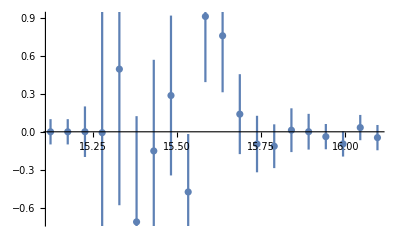

```mathematica
If[UseErr,
Residuals=TheFit[Ind]["FitResiduals"];
ResidualsAndErr[TheTab_]:=Table[{{Part[TheTab,Ind2,XCol],Part[Residuals,Ind2]},ErrorBar[Part[TheTab,Ind2,YErrCol]]},{Ind2,Length[TheTab]}];
ErrorListPlot[ResidualsAndErr[TheData[Ind]],PlotRange->All]
]
```

```mathematica
MyOffset=-15.2;
ExpPoints=300;
ExpTab=Table[{t+MyOffset,TheFit[Ind][t]},{t,MinTime,MaxTime,(MaxTime-MinTime)/ExpPoints}];
Export["D:/Temp/Counts-L-fit.txt",SetPrecision[ExpTab,6],"Table"]
```

D:/Temp/Counts-L-fit.txt